```mathematica
(* notebook to find energy density of stringbit *)
```

```mathematica
ClearAll[LoadEigenEnergies,LoadAndBucketEnergies,PlotEnergyBuckets];
DataFolder = NotebookDirectory[]<>"../data/";
Format[energy,StandardForm]="E";

(*Bucketed = 1 means already bucketed (default)
Bucketed = 0 means not yet
Bucketed > 1=n mean not yet and require split the data into n buckets.
*)
Options[LoadEigenEnergies]={Folder->DataFolder,Bucketed->1,  Single->False,ColorN->Infinity};
LoadEigenEnergies[s_,M_,opts:OptionsPattern[]]:=Module[{file,data},
file = "EEs="<> ToString[s] <> "M="<>ToString[M];
If[OptionValue[ColorN]≠Infinity, file = file <> "N="<>ToString[OptionValue[ColorN]]];
If[OptionValue[Single], file = file <>"s"];
If[OptionValue[Bucketed]==1, file = file <>"g"];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
If[OptionValue[Bucketed]≠1,data=Flatten[data]];
If[OptionValue[Bucketed]>1,data=BucketData[data,OptionValue[Bucketed]]];
(*If[OptionValue[Bucketed]≠0,data = RebucketData[data]];*)
Return[data];
];

ClearAll[BucketData];
BucketData[list_,n_]:=Module[{min,max,delta,res,pos,i},
min = First[list];
max=Last[list];
delta = (max-min)/n;
res = Table[{i*delta + min,0},{i,0,n}];

For[i=1,i≤Length[list],i++,
pos =Floor[(list[[i]]-min)/delta + 1.5];
res[[pos,2]]=res[[pos,2]]+1;
];

Return[res]
];

(*re-do the bucket. Merge buckets with zero data with their neibough*)
ClearAll[RebucketData]
RebucketData[data_]:=Module[{i,j,res={},lastZ=-1,ave,ret={}},
For[i=1,i≤Length[data],i++,
If[data[[i,2]]==0 && lastZ==-1,lastZ=i];

If[data[[i,2]]≠ 0,
If[lastZ>0,
ave=Sum[data[[j,1]],{j,lastZ,i-1}]/(i-lastZ);
AppendTo[res,{ave,0}];
lastZ=-1;
];

AppendTo[res, data[[i]]];
];
];

If[lastZ≠-1,
ave=Sum[data[[j,1]],{j,lastZ,Length[data]}]/(Length[data]-lastZ+1);
AppendTo[res,{ave,0}];
];
(*For[i=1,i≤ Length[res],i++,
If[res[[i,2]]==0 && i>1 && i <Length[res],
ret[[-1,1]]=(Last[ret][[1]]+res[[i,1]])/2;
AppendTo[ret,{ (res[[i,1]]+res[[i+1,1]])/2,res[[i+1,2]]}];
i=i+1,
AppendTo[ret,res[[i]]]
];
];

Print["tot3=",Sum[ret[[i]],{i,Length[ret]}]];*)

Return[res]
];

ClearAll[AverageEnergy];
Options[AverageEnergy]=Join[Options[LoadEigenEnergies],{}];
AverageEnergy[s_,M_, opts:OptionsPattern[]]:=Module[{data,data2,i,tot,count},
data = LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
If[OptionValue[Bucketed]==0,
Return[Mean[data]],
tot=0;count=0;
For[i=1,i≤Length[data],i++,
tot += data[[i,1]] * data[[i,2]];
count += data[[i,2]]
];
Return[tot/count]
];
];

ClearAll[EnergyVariance];
Options[EnergyVariance]=Join[Options[LoadEigenEnergies],{}];
EnergyVariance[s_,M_, opts:OptionsPattern[]]:=Module[{data,data2},
data = LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
data2=Table[data[[i]]^2,{i,1,Length[data]}];
Return[Mean[data2]-Mean[data]^2];
];

LoadAndBucketEnergies[s_,M_,n_]:=Module[{data,maxE,delta, buckets,i,pos},
data=LoadEigenEnergies[s,M];
maxE=N[4*s*Cot[Pi/(2M)]];
delta=2*maxE/n;
buckets=ConstantArray[0,n];
pos=Floor[(data+maxE)/delta] + 1;
For[i=1,i≤Length[pos],i++,
buckets[[pos[[i]]]]=buckets[[pos[[i]]]]+1;
];

Return[{Table[Chop[-maxE+delta*(i-0.5)],{i,1,n}],buckets}]
];

ClearAll[NormalizeData];
Options[NormalizeData]={NormScale->False};
NormalizeData[data_,opts:OptionsPattern[]]:=Module[{tot,delta,ndata={},i},
(* normalize data *)
tot=Sum[data[[i,2]],{i,1,Length[data]}];
delta =data[[2,1]]-data[[1,1]];
If[OptionValue[NormScale],
ndata=Table[{data[[i,1]],data[[i,2]]/(delta*tot)},{i,1,Length[data]}],
ndata=Table[{data[[i,1]],data[[i,2]]/delta},{i,1,Length[data]}]
];

(*Print["ndata size=",tot];*)
(*For[i=1,i≤Length[data],i++,
If[i==1, 
delta = data[[2,1]]-data[[1,1]],
If[i==Length[data],
delta = data[[i,1]]-data[[i-1,1]],
delta = (data[[i+1,1]]-data[[i-1,1]])/2
]
];

If[OptionValue[NormScale],
AppendTo[ndata, {data[[i,1]],data[[i,2]]/(tot*delta)}],
AppendTo[ndata, {data[[i,1]],data[[i,2]]/(delta)}];
];
];*)

Return[ndata]
];

ClearAll[GaussianFit];
GaussianFit[data_,tot_]:=Module[{lmf},
lmf=NonlinearModelFit[data[[2;;Length[data]-2]], 
tot*Am/(sigma*Sqrt[2*Pi])*Exp[-(x-mu)^2/(2*sigma^2)],
{mu, sigma,Am}, {x}];
Return[lmf]
];

ClearAll[PlotEnergyBuckets];
Options[PlotEnergyBuckets]=Join[Options[LoadEigenEnergies],Options[NormalizeData],{GlobalFit->False,PrintFit->False}];
PlotEnergyBuckets[s_,M_,opts:OptionsPattern[]]:=Module[{data,tot,ndata={},fit,p1,p2,p3,i,range1,range2},
data=LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
tot=Sum[data[[i,2]],{i,1,Length[data]}];
(* normalize data *)
ndata = NormalizeData[data,FilterRules[{opts},Options[NormalizeData]]];
range1=ndata[[1,1]]-.1;
range2 = Last[ndata][[1]]+0.1;
(*Print["range=", range];*)
p1=ListPlot[ndata,AxesLabel->{"E", "ρ(E)"}(*,PlotLegends->{"Numerical"},PlotLabels->{"M="<>ToString[M]}*)];
If[OptionValue[GlobalFit],
If[OptionValue[NormScale],
p2=Plot[1/Sqrt[2*Pi*SigmaFit[M]^2]Exp[-(x-MuFit[M])^2/(2*SigmaFit[M]^2)],{x, range1,range2}],
p2=Plot[tot/Sqrt[2*Pi*SigmaFit[M]^2]Exp[-(x-MuFit[M])^2/(2*SigmaFit[M]^2)],{x, range1,range2}]
],

If[OptionValue[NormScale],
fit=GaussianFit[ndata,1],
fit=GaussianFit[ndata,tot];
];

If[OptionValue[PrintFit],Print[fit["ParameterConfidenceIntervalTable"]]];
p2=Plot[fit[x],{x, range1,range2}]
];

Show[p1,p2]
];

ClearAll[FitEnergyData];
Options[FitEnergyData]=Join[Options[LoadEigenEnergies],Options[NormalizeData],{}];
FitEnergyData[s_, M_,opts:OptionsPattern[]]:=Module[{data, lmf, tot,ndata={},delta,i},
data=LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
tot=Sum[data[[i,2]],{i,1,Length[data]}];
ndata = NormalizeData[data,FilterRules[{opts},Options[NormalizeData]]];
If[OptionValue[NormScale],
lmf=GaussianFit[ndata,1],
lmf=GaussianFit[ndata,tot];
];

Return[{mu,sigma,Am}/.lmf["BestFitParameters"]];
];

ClearAll[FindN2Correction];
FindN2Correction[s_,M_,Nlist_]:=Module[{i,fit,largeN,res={},lmf1,lmf2,p2,p1,pp1,pp2,p1a,p2a},
For[i=1,i≤Length[Nlist],i++,
fit=FitEnergyData[s,M,ColorN->Nlist[[i,1]],Bucketed->Nlist[[i,2]]];
AppendTo[res, Join[{1/Nlist[[i,1]]^2},fit]];
];

(*lmf1=NonlinearModelFit[res[[All,{1,2}]], A+B/x^2+cc/x^4,{A,B,cc}, {x}];
lmf2=NonlinearModelFit[res[[All,{1,3}]], A+B/x^2+cc/x^4,{A,B,cc}, {x}];*)
lmf1=NonlinearModelFit[res[[All,{1,2}]], A+B*x,{A,B}, {x}];
lmf2=NonlinearModelFit[res[[All,{1,3}]], A+B*x,{A,B}, {x}];
Print[lmf1["ParameterConfidenceIntervalTable"]];
Print[lmf2["ParameterConfidenceIntervalTable"]];
p1=ListPlot[res[[All,{1,2}]]];
p2=ListPlot[res[[All,{1,3}]]];
(*p1a=Plot[lmf1[x],{x,First[Nlist][[1]],Last[Nlist][[1]]}];
p2a=Plot[lmf2[x],{x,First[Nlist][[1]],Last[Nlist][[1]]}];*)
p1a=Plot[lmf1[x],{x,0,First[Nlist][[1]]}];
p2a=Plot[lmf2[x],{x,0,First[Nlist][[1]]}];
Return[{Show[p1,p1a],Show[p2,p2a]}]
];

ClearAll[FindBestBucket];
FindBestBucket[s_,M_,colorN_,minBucket_,maxBucket_,single_:False]:=Module[{i,data,tot,fit,besti=0,best,delta},
best={};
For[i=minBucket,i≤maxBucket,i++,
data=LoadEigenEnergies[s,M,Bucketed->i,ColorN->colorN,Single->single];
tot=Sum[data[[i,2]],{i,Length[data]}];
delta=data[[2,1]]-data[[1,1]];
data=Table[{data[[j,1]],data[[j,2]]/delta},{j,Length[data]}];
fit=GaussianFit[data,tot];
If[fit["ParameterConfidenceIntervalTableEntries"][[3,1]]<0.9,Continue[]];
If[besti==0 || fit["ParameterConfidenceIntervalTableEntries"][[1,2]]<best[[1,2]],
best=fit["ParameterConfidenceIntervalTableEntries"];besti=i;
];
];

Return[{besti,best}]
];

FindBestBucketBatch[s_,M_,Nlist_,minBucket_,maxBucket_]:=Module[{i,res,ret={}},
For[i=1,i≤Length[Nlist],i++,
res=FindBestBucket[s,M,Nlist[[i]],minBucket,maxBucket];
AppendTo[ret,{Nlist[[i]],res[[1]]}];
Print["N=",Nlist[[i]],", res=",res];
];

Return[ret]
];

FindBestBucketBatchM[s_,MList_,minBucket_,maxBucket_]:=Module[{i,res,ret={}},
For[i=1,i≤Length[MList],i++,
res=FindBestBucket[s,MList[[i]],Infinity,minBucket,maxBucket,True];
AppendTo[ret,{MList[[i]],res[[1]]}];
Print["M=",MList[[i]],", res=",res];
];

Return[ret]
];
```

```mathematica
FindBestBucketBatch[1,12,{12,13,14,20,50,Infinity}, 20,60]
```

N=12, res={42,{{2.97615,0.13942,{2.69366,3.25864}},{11.2048,0.139678,{10.9218,11.4879}},{0.99604,0.0107397,{0.974279,1.0178}}}}

N=13, res={22,{{3.02952,0.136605,{2.74131,3.31773}},{11.2514,0.136958,{10.9625,11.5404}},{0.997928,0.0105018,{0.975771,1.02008}}}}

N=14, res={33,{{3.07968,0.152112,{2.7681,3.39127}},{11.1956,0.152408,{10.8834,11.5078}},{0.997293,0.0117423,{0.97324,1.02135}}}}

N=20, res={31,{{3.20423,0.190365,{2.81293,3.59553}},{11.2742,0.190898,{10.8818,11.6666}},{1.00105,0.0146519,{0.970936,1.03117}}}}

N=50, res={25,{{3.32601,0.277147,{2.74789,3.90412}},{11.2328,0.281092,{10.6465,11.8192}},{1.00185,0.0215093,{0.956978,1.04671}}}}

N=∞, res={48,{{3.30701,0.348634,{2.60392,4.01009}},{11.2547,0.356058,{10.5366,11.9727}},{1.00346,0.0271128,{0.948783,1.05814}}}}

{{12,42},{13,22},{14,33},{20,31},{50,25},{∞,48}}

| Estimate | Standard Error | Confidence Interval
A | 3.32723 | 0.00968533 | {3.30034,3.35412}
B | -49.8845 | 2.20578 | {-56.0088,-43.7603}

| Estimate | Standard Error | Confidence Interval
A | 11.254 | 0.0196388 | {11.1995,11.3085}
B | -5.29881 | 4.47263 | {-17.7168,7.1192}

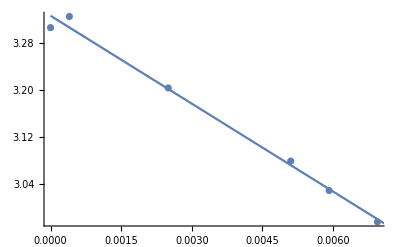
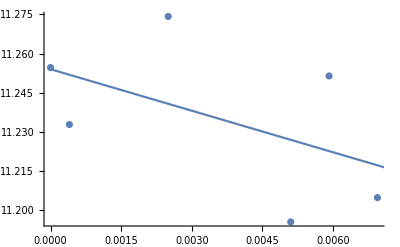

| Estimate | Standard Error | Confidence Interval
A | 3.3753 | 0.00694791 | {3.35744,3.39316}
B | -59.8039 | 1.69544 | {-64.1622,-55.4457}

| Estimate | Standard Error | Confidence Interval
A | 11.5396 | 0.03563 | {11.4481,11.6312}
B | 20.1144 | 8.69452 | {-2.2356,42.4644}

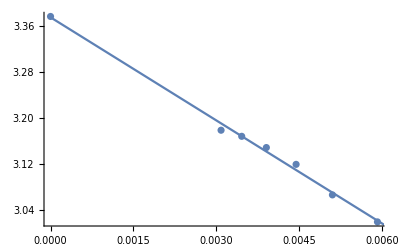
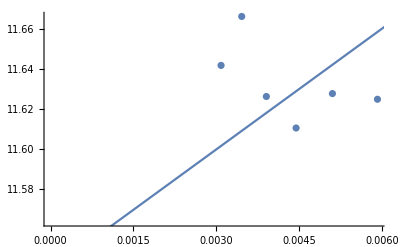

| Estimate | Standard Error | Confidence Interval
A | 3.37785 | 0.00161252 | {3.37371,3.382}
B | -59.5818 | 0.466115 | {-60.78,-58.3836}

| Estimate | Standard Error | Confidence Interval
A | 12.0191 | 0.00781697 | {11.999,12.0392}
B | -6.86268 | 2.25958 | {-12.6711,-1.05426}

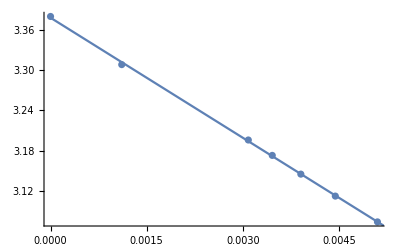
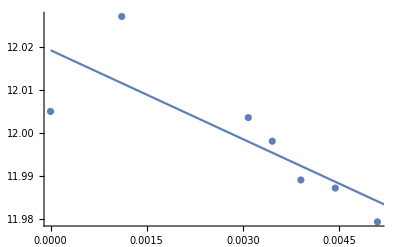

| Estimate | Standard Error | Confidence Interval
A | 3.23972 | 0.064475 | {3.03453,3.44491}
B | 2.22331 | 29.7161 | {-92.3466,96.7933}
cc | -6767.76 | 3290.9 | {-17240.9,3705.35}

| Estimate | Standard Error | Confidence Interval
A | 11.842 | 0.180313 | {11.2682,12.4159}
B | -87.3661 | 83.1053 | {-351.844,177.112}
cc | 8595.36 | 9203.46 | {-20694.1,37884.9}

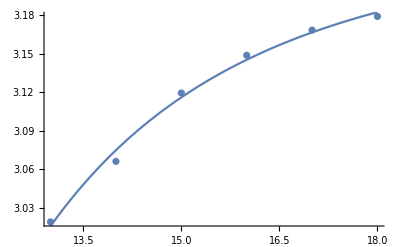
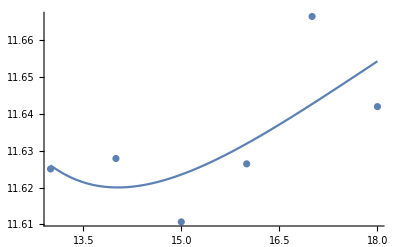

| Estimate | Standard Error | Confidence Interval
A | 3.36971 | 0.00253886 | {3.36163,3.37778}
B | -54.4952 | 1.77305 | {-60.1378,-48.8526}
cc | -721.291 | 285.476 | {-1629.8,187.222}

| Estimate | Standard Error | Confidence Interval
A | 12.0427 | 0.00473404 | {12.0276,12.0577}
B | -14.3111 | 3.30609 | {-24.8326,-3.78969}
cc | 361.717 | 532.308 | {-1332.32,2055.76}

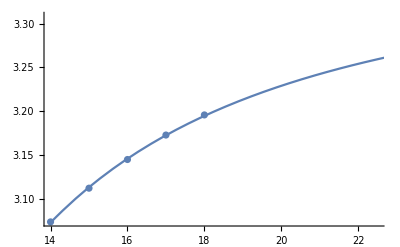
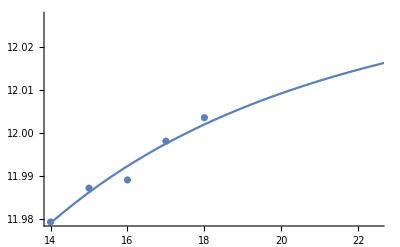

```mathematica
(*(* Results: {{12,42},{13,22},{14,33},{20,31},{50,25},{∞,48}} *)
FindBestBucketBatch[1,12,{12,13,14,20,50,Infinity}, 20,60]*)
FindN2Correction[1,12,{{12,42},{13,22},{14,33},{20,31},{50,25},{Infinity,48}}]

(*(* results: {{13,31},{14,41},{15,48},{16,29},{17,29},{18,39},{Infinity, 50}}*)
FindBestBucketBatch[1,13,{13,14,15,16,17,18}, 20,60]*)
FindN2Correction[1,13,{{13,31},{14,41},{15,48},{16,29},{17,29},{18,39},{Infinity, 50}}]

(*(* results: {{14,81},{15,54},{16,53},{17,52},{18,52},{30,65},{Infinity, 57}} *)
FindBestBucketBatch[1,14,{14,15,16,17,18,30,Infinity}, 50,90]*)
FindN2Correction[1,14,{{14,81},{15,54},{16,53},{17,52},{18,52},{30,65},{Infinity,57}}]

(*PlotEnergyBuckets[1,13,ColorN->18,Bucketed->39,PrintFit->True]
PlotEnergyBuckets[1,13,ColorN->17,Bucketed->29,PrintFit->True]*)

(*PlotEnergyBuckets[1,13,ColorN->13,Bucketed->31,PrintFit->True]
PlotEnergyBuckets[1,12,Bucketed->48,PrintFit->True]
PlotEnergyBuckets[1,12,ColorN->12,Bucketed->42,PrintFit->True]
PlotEnergyBuckets[1,11,GlobalFit->False,ColorN ->11,Bucketed->26,PrintFit->True]
PlotEnergyBuckets[1,11,GlobalFit->False,Bucketed->40,PrintFit->True]*)

(*FindN2Correction[1,11,{11,20,21,22,25,30,40,50,100,200,300}]*)
```

{{18,3.4181,13.3317,1.00289},{19,3.42213,13.6227,1.00244},{20,3.43047,13.9431,1.00298},{21,3.43463,14.2168,1.00264},{22,3.43683,14.4907,1.00234},{23,3.44396,14.7692,1.00236},{24,3.44855,15.0412,1.00228},{25,3.45251,15.3056,1.00219},{26,3.45506,15.566,1.0021},{27,3.45914,15.8248,1.0021},{28,3.46225,16.0781,1.00212},{29,3.46331,16.3259,1.00204},{30,3.46714,16.5717,1.002},{31,3.46985,16.8133,1.00194}}

{b→3.55398,c→2.81351,d→6.37161}

{b→3.5423,c→2.26028}

{a→0.26703,b→8.59355}

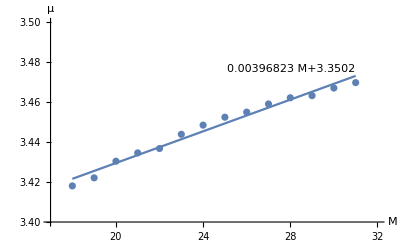

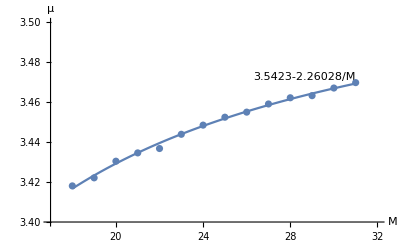

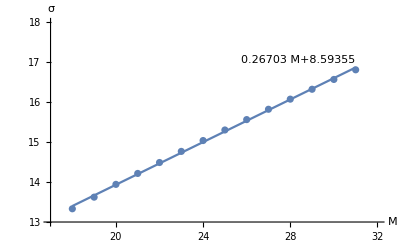

```mathematica
minM=18;
maxM = 31;
param=Table[Join[{m},FitEnergyData[1,m]],{m,minM,maxM}]
param1=param[[All,{1,2}]];
param2=param[[All,{1,3}]];
tfit1b=NonlinearModelFit[param1, a*M+b,{ b,a}, {M}];
tfit1=NonlinearModelFit[param1, b-c/M,{ b,c}, {M}];
tfit1c=NonlinearModelFit[param1, b-c/M+d/M^2,{ b,c,d}, {M}];
tfit2=NonlinearModelFit[param2, a*M+b,{a, b}, {M}];
tfit1c["BestFitParameters"]
tfit1["BestFitParameters"]
tfit2["BestFitParameters"]
SigmaFit[M_]:=tfit2[M];
MuFit[M_]:=tfit1[M];

tplot1=Plot[tfit1[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1],Above],AxesLabel->{"M", "μ"},PlotRange->{{minM-1,maxM+1},{3.4,3.5}}];
tplot2=Plot[tfit2[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit2],Above],AxesLabel->{"M", "σ"},PlotRange->{{minM-1,maxM+1},{13,18}}];
tplot1b=Plot[tfit1b[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1b],Above],AxesLabel->{"M", "μ"},PlotRange->{{minM-1,maxM+1},{3.4,3.5}}];
tplot1c=Plot[tfit1c[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1c],Above],AxesLabel->{"M", "μ"},PlotRange->{{minM-1,maxM+1},{3.4,3.5}}];
s1=Show[tplot1b,ListPlot[param[[All,{1,2}]]]]
(*s1c=Show[tplot1c,ListPlot[param[[All,{1,2}]]]]*)
s2=Show[tplot1,ListPlot[param[[All,{1,2}]]]]
s3=Show[tplot2,ListPlot[param[[All,{1,3}]]]]
(*Export["mu.pdf",s1];
Export["fit-mu.pdf",s2];
Export["fit-sigma.pdf",s3];*)
Clear[s1,s2,s3,s1c]
```

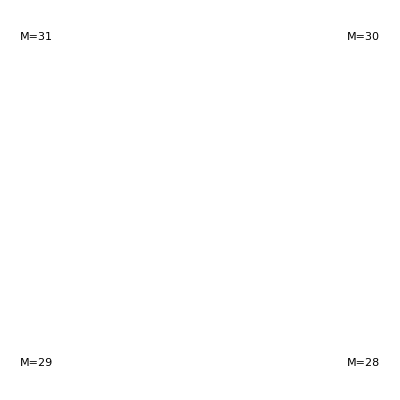

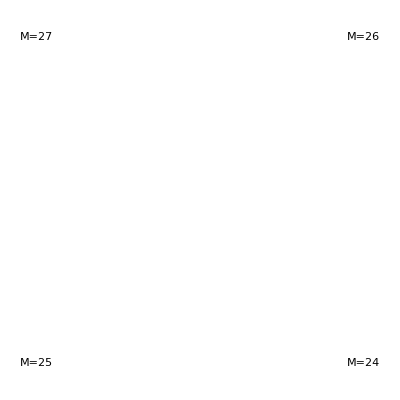

```mathematica
(*minM=19;
maxM=31;
For[ti=minM,ti≤maxM,ti++,
plot=Labeled[PlotEnergyBuckets[1,ti],"M="<>ToString[ti]];
Export["E-density-M"<>ToString[ti]<>".pdf",plot]
]
Clear[ti];*)
rescale=True;
g1=Labeled[PlotEnergyBuckets[1,31,NormScale->rescale],"M=31"];
g2=Labeled[PlotEnergyBuckets[1,30,NormScale->rescale],"M=30"];
g3=Labeled[PlotEnergyBuckets[1,29,NormScale->rescale],"M=29"];
g4=Labeled[PlotEnergyBuckets[1,28,NormScale->rescale],"M=28"];
GraphicsGrid[{{g1,g2},{g3,g4}}]

g1=Labeled[PlotEnergyBuckets[1,27,NormScale->rescale],"M=27"];
g2=Labeled[PlotEnergyBuckets[1,26,NormScale->rescale],"M=26"];
g3=Labeled[PlotEnergyBuckets[1,25,NormScale->rescale],"M=25"];
g4=Labeled[PlotEnergyBuckets[1,24,NormScale->rescale],"M=24"];
GraphicsGrid[{{g1,g2},{g3,g4}}]

ClearAll[g1,g2,g3,g4];
```

```mathematica
(* functions for thermaldynamics *)
ClearAll[LoadThermalData];
Options[LoadThermalData]={Folder->DataFolder,FiniteN->False,DataType->"Z"};
LoadThermalData[s_,M_,T0_,opts:OptionsPattern[]]:=Module[{file,data,x,y},
If[OptionValue[FiniteN],
file = "THs="<> ToString[s] <> "N="<>ToString[M]<>"T0="<>ToString[T0],
file = "THs="<> ToString[s] <> "M="<>ToString[M]<>"T0="<>ToString[T0]
];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
x=1;

Switch[OptionValue[DataType],
"Z",y=2,
"E",y=3,
"S",y=4,
"ES",x=3;y=4,
"SE",x=4;y=3,
_, Print["DataType ", OptionValue[DataType], " is not supported!"];Return[]
];

Return[Table[{data[[i, x]],data[[i,y]]},{i,1,Length[data]}]];
];

ClearAll[FitESData];
FitESData[s_,N_,T0_]:=Module[{data,lmf,p1,p2},
data=LoadThermalData[s,N,T0,FiniteN->True,DataType->"ES"];
(*Print[data];*)

lmf=NonlinearModelFit[data, Sqrt[a*x+b]-c,{a,b,c}, {x}];

Print[lmf["ParameterConfidenceIntervalTable"]];
(*p1=PlotThermalForN[s,N,T0,FiniteN->True,DataType->"ES"];
p2=Plot[lmf[x],{x,Last[data][[1]],First[data][[2]]}];
Return[Show[p1,p2]]*)
];

Options[LoadFluctuation]={Folder->DataFolder};
LoadFluctuation[s_,M_,opts:OptionsPattern[]]:=Module[{file,data},
file = "FLs="<> ToString[s] <> "M="<>ToString[M];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
Return[data];
];

MaxEnergy[s_,M_]:=4*s*Cot[Pi/(2*M)];
MinEnergy[s_,M_]:=If[Mod[M,2]==1,
-4*s*Cot[Pi/(2*M)],
If[Mod[M,4]==2,-8*Cot[Pi/M],-4*(Cot[Pi/(M-2)]+Cot[Pi/M+2])]
];

AveEnergyByZ[s_,M_,T0_,beta_]:=-T0^2*beta*SigmaFit[M]^2+1/Sqrt[2]*(M+T0*MuFit[M])-(Erf[(MaxEnergy[s,M]-MuFit[M])/(Sqrt[2]SigmaFit[M])+T0*beta*SigmaFit[M]/2]+Erf[(MuFit[M]-MinEnergy[s,M])/(Sqrt[2]SigmaFit[M])-T0*beta*SigmaFit[M]/2])^(-1)*1/Sqrt[Pi]*T0*SigmaFit[M]*(Exp[-((MaxEnergy[s,M]-MuFit[M])/(Sqrt[2]SigmaFit[M])+T0*beta*SigmaFit[M]/2)^2]-Exp[-((MuFit[M]-MinEnergy[s,M])/(Sqrt[2]SigmaFit[M])-T0*beta*SigmaFit[M]/2)^2]);

LogZ[s_,M_,T0_,beta_]:=1/2*T0^2*beta^2*SigmaFit[M]^2-1/Sqrt[2]*beta*(M+T0*MuFit[M])+(M-1)*Log[2]+Log[0.7261768]+Log[Erf[(MaxEnergy[s,M]-MuFit[M])/(Sqrt[2]SigmaFit[M])+T0*beta*SigmaFit[M]/2]+Erf[(MuFit[M]-MinEnergy[s,M])/(Sqrt[2]SigmaFit[M])-T0*beta*SigmaFit[M]/2]];

ClearAll[PlotThermalData];
Options[PlotThermalData]=Join[Options[LoadThermalData],{MaxBeta->0}];
PlotThermalData[s_,M_,T0_,opts:OptionsPattern[]]:=Module[
{data,labelX, labelY,maxBeta,p0,p1},
data = LoadThermalData[s,M,T0,FilterRules[{opts},Options[LoadThermalData]]];
If[OptionValue[MaxBeta]>0,maxBeta=OptionValue[MaxBeta],maxBeta = Last[data][[1]]];

labelX="β";
Switch[OptionValue[DataType],
 "Z",labelY="ln(Z)",
"E", labelY = "E",
"S",labelY = "S",
"ES",labelX="E";labelY = "S",
"SE",labelX="S";labelY = "E"
];

p0=ListPlot[data,AxesLabel->{labelX, labelY},PlotRange->{{0,maxBeta},Automatic}];

If[OptionValue[DataType]=="Z",
p1=Plot[LogZ[s,M,T0,beta],{beta,0,maxBeta}];Return[Show[p0,p1]],
If[OptionValue[DataType]=="E",
p1=Plot[AveEnergyByZ[s,M,T0,beta],{beta,0,maxBeta}];Return[Show[p0,p1]]
]
];

Return[p0]
]

ClearAll[PlotThermalForN];
Options[PlotThermalForN]=Join[Options[LoadThermalData],{}];
PlotThermalForN[s_,N_,T0_,opts:OptionsPattern[]]:=Module[{data,labelX,labelY},
data = LoadThermalData[s,N,T0,FilterRules[{opts},Options[LoadThermalData]]];
labelX="β";
Switch[OptionValue[DataType],
 "Z",labelY="ln(Z)",
"E", labelY = "E",
"S",labelY = "S",
"ES",labelX="E";labelY = "S",
"SE",labelX="S";labelY = "E"
];

Return[ListPlot[data,AxesLabel->{labelX, labelY}]]
]

ClearAll[PlotThermalForBeta];
Options[PlotThermalForBeta]=Join[Options[LoadThermalData],{}];
PlotThermalForBeta[s_,beta_,T0_,minN_,maxN_,opts:OptionsPattern[]]:=Module[
{data={},tmpdata,i,label},

For[i=minN,i≤maxN,i++,
tmpdata = LoadThermalData[s,i,T0,FilterRules[{opts},Options[LoadThermalData]]];
AppendTo[data,{i,SelectFirst[tmpdata,#[[1]]==beta &][[2]]}]
];

Switch[OptionValue[DataType],
 "Z",label="ln(Z)",
"E", label = "E",
"S",label = "S";
];

Return[ListPlot[data,AxesLabel->{"N", label},Joined->True]]
]

PlotFluctuation[s_,M_]:=Module[{data2,data,Z2},
data = LoadFluctuation[s,M];
Z2 = data[[1,2]]^2;
data2 = Table[{data[[i, 1]],(data[[i,2]]^2+data[[i,3]]^2)/Z2},{i,2,Length[data]}];
Return[ListPlot[data2]]
]
```

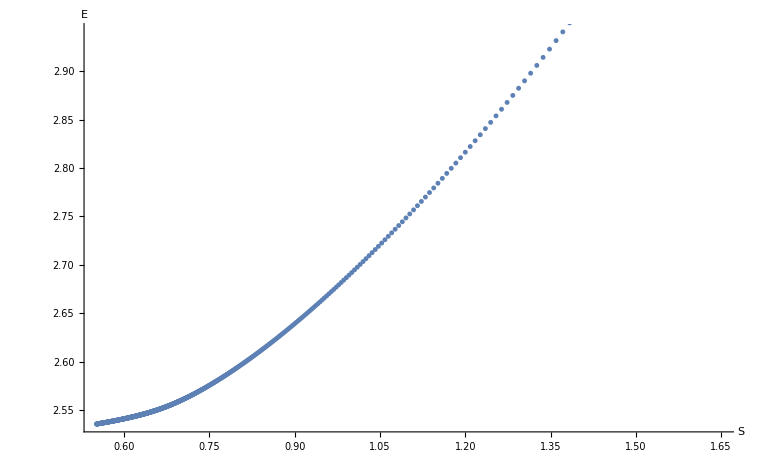

```mathematica
(*PlotThermalData[1,19,1,DataType->"Z",MaxBeta->1]
PlotThermalData[1,19,1,DataType->"E",MaxBeta->1]
PlotThermalData[1,19,1,DataType->"S",MaxBeta->1]
PlotThermalData[1,19,1,DataType->"ES"]*)

(*FitESData[1,12,1]*)

(*PlotThermalForBeta[1,2.0, 1,5,12,FiniteN->True,DataType->"Z"]
PlotThermalForBeta[1,1.0, 1,5,12,FiniteN->True,DataType->"E"]
PlotThermalForBeta[1,0.5, 1,5,12,FiniteN->True,DataType->"S"]
PlotThermalForBeta[1,0.1, 1,5,12,FiniteN->True,DataType->"Z"]
PlotThermalForBeta[1,0.01, 1,5,12,FiniteN->True,DataType->"Z"]*)

(*PlotThermalForN[1,12,1,FiniteN->True,DataType->"Z"]
PlotThermalForN[1,12,1,FiniteN->True,DataType->"E"]
PlotThermalForN[1,12,1,FiniteN->True,DataType->"S"]*)
PlotThermalForN[1,12,1,FiniteN->True,DataType->"SE"]
```

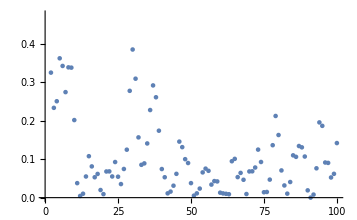

```mathematica
Show[PlotFluctuation[1,19]]
```

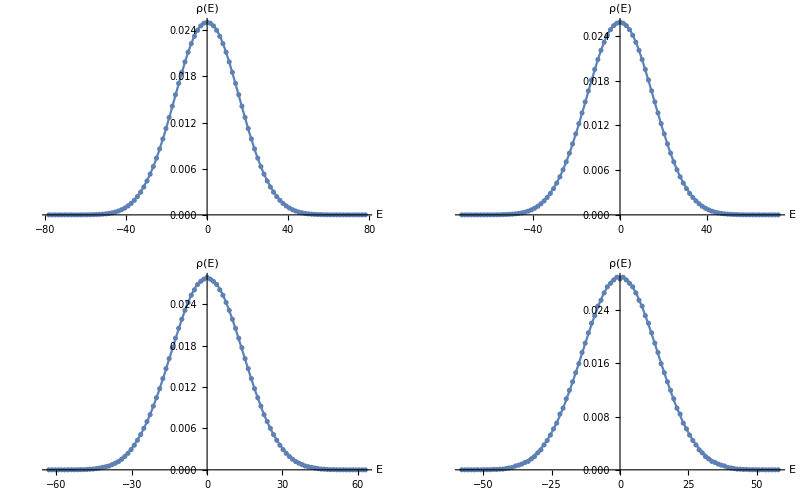

```mathematica
rescale=True;
g1=PlotEnergyBuckets[1,31,Single->True,NormScale->rescale];
g2=PlotEnergyBuckets[1,29,Single->True,NormScale->rescale];
g3=PlotEnergyBuckets[1,27,Single->True,NormScale->rescale];
g4=PlotEnergyBuckets[1,25,Single->True,NormScale->rescale];
g5=PlotEnergyBuckets[1,23,Single->True,NormScale->rescale];
g6=PlotEnergyBuckets[1,21,Single->True,NormScale->rescale];

GraphicsGrid[{{g1,g2},{g4,g5}}]
ClearAll[g1,g2,g3,g4,g5,g6];
```

{b→-0.000196684,c→-0.00407415}

{a→0.280089,b→7.32241}

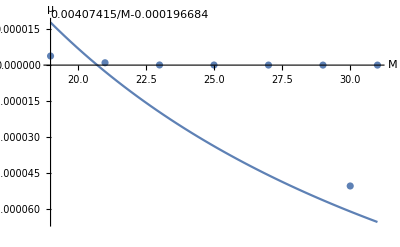

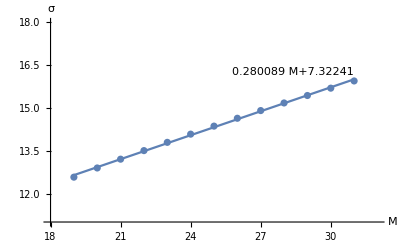

$Aborted

```mathematica
minM=19;
maxM = 31;
param=Table[Join[{m},FitEnergyData[1,m,Single->True]],{m,minM,maxM}];
param1=param[[All,{1,2}]];
param2=param[[All,{1,3}]];
tfit1=NonlinearModelFit[param1, b-c/M,{ b,c}, {M}];
tfit2=NonlinearModelFit[param2, a*M+b,{a, b}, {M}];

tfit1["BestFitParameters"]
tfit2["BestFitParameters"]

tplot1=Plot[tfit1[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1],Above],AxesLabel->{"M", "μ"}];
tplot2=Plot[tfit2[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit2],Above],AxesLabel->{"M", "σ"},PlotRange->{{18,32},{11,18}}];
tplot1b=Plot[tfit1b[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1b],Above],AxesLabel->{"M", "μ"}];

Show[tplot1,ListPlot[param[[All,{1,2}]]]]
(*Export["fit-mu.pdf",%];*)
Show[tplot2,ListPlot[param[[All,{1,3}]]]]
(*Export["fit-sigma-single.pdf",%];*)
```

{{8,0.000767269,11.5461,1.00395},{9,0.0000591296,12.204,1.00246},{10,0.00746691,12.8371,1.0024},{11,4.25107×10^-6,13.5664,1.00448},{12,3.25589×10^-6,14.13,1.00356}}

{b→0.00142013,c→-0.00235164}

{a→0.653022,b→6.3265}

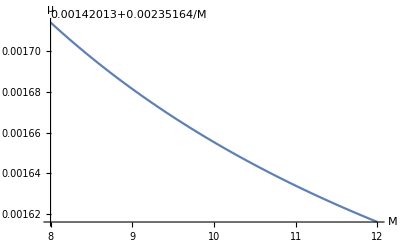

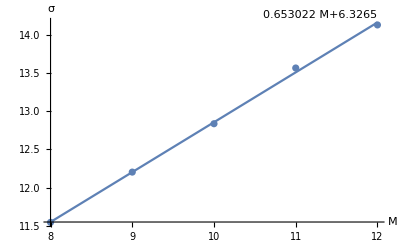

```mathematica
(* results: {{8,20},{9,32},{10,23},{11,28},{12,24}} *)
(*FindBestBucketBatchM[2, {8,9,10,11,12},20,60]*)

minM=8;
maxM = 12;
bestBuckets={{8,20},{9,32},{10,23},{11,28},{12,24}};
param=Table[Join[{m},FitEnergyData[2,m,Single->True,Bucketed->bestBuckets[[m-minM+1,2]]]],{m,minM,maxM}]
param1=param[[All,{1,2}]];
param2=param[[All,{1,3}]];
tfit1=NonlinearModelFit[param1, b-c/M,{ b,c}, {M}];
tfit2=NonlinearModelFit[param2, a*M+b,{a, b}, {M}];

tfit1["BestFitParameters"]
tfit2["BestFitParameters"]

tplot1=Plot[tfit1[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1],Above],AxesLabel->{"M", "μ"}];
tplot2=Plot[tfit2[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit2],Above],AxesLabel->{"M", "σ"}];

Show[tplot1,ListPlot[param[[All,{1,2}]]]]
(*Export["fit-mu.pdf",%];*)
Show[tplot2,ListPlot[param[[All,{1,3}]]]]
(*Export["fit-sigma-single.pdf",%];*)
```

```mathematica
AA={a,b}/.{a->0.28008891978717937,b->7.322405297879064}
BB={a,b}/.{a->0.6530218130283911,b->6.326502785560906};
BB[[1]]/AA[[1]]
BB[[2]]/AA[[2]]
```

{0.280089,7.32241}

2.33148

0.863992